## Definitions of Functions

IMPORTANT NOTE: This notebook is to be used in conjunction with the Perl script ParseModelFile.pl which - as the name suggests - parses a libSVM model file and creates a Mathematica notebook. These Mathematica notebooks make the following definitions:
	k: kernel function, takes two vectors of the same lengths as arguments; note: even in the 1D case, the arguments have to be lists of length 1
	b: real number, constant offset of the discriminant/regression function
	alphay: list of real values corresponding to the product of class labels and Lagrange multipliers
	xlist: list of support vectors
Only if these symbols are defined and comply with the above requirements, the functions defined below will work. The best way is simply to load the Mathematica notebooks created with ParseModelFile.pl. Presently, ParseModelFile.pl can handle all five types of SVMs libSVM implements (C-SVC, nu-SVC, one-class-SVM, epsilon-SVR, nu-SVR). It can handle the four built-in kernels, but it does not support pre-computed kernel matrices.

```mathematica
(* function for indicating support vectors *)
PlotSupportVectors[]:=Table[Graphics[Circle[xlist[[i]],0.018]],{i,1,Length[xlist]}];

(* SVM discriminant/regression function *)
SVM[x_]:=Sum[alphay[[i]]*k[xlist[[i]],x],{i,1,Length[alphay]}]+b;

(* function for plotting a 2D data set and its SVM classification function together, can also be used for the one-class-SVM *)      
PlotSVC[data_]:=Module[{g1,g2,g3},
	g1=ContourPlot[SVM[{x,y}],{x,-0.08,1.08},{y,-0.08,1.08},PlotPoints->51,Contours->{0},ContourShading->{LightBlue,LightPink},DisplayFunction->Identity];
	g2=ClassificationDataPlot[data];
	g3=PlotSupportVectors[];
	Show[g1,g2,g3,AspectRatio->1,Frame->True,PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->{500,Automatic},DisplayFunction->$DisplayFunction]];

(* function for plotting a 2D data set and its SVM classification function together (with 9 contour levels), can also be used for the one-class-SVM *)      
PlotSVCContour[data_]:=Module[{g1,g2,g3},
	g1=ContourPlot[SVM[{x,y}],{x,-0.08,1.08},{y,-0.08,1.08},Contours->{-8,-7,-6,-5-4,-3,-2,-1,0,1,2,3,4,5,6,7,8},PlotPoints->51,ColorFunctionScaling->False,ColorFunction->(If[#<0,Blend[{White,Blue},Abs[#/10]],Blend[{White,Red},Abs[#/10]]]&),DisplayFunction->Identity];
	g2=ClassificationDataPlot[data];
	g3=PlotSupportVectors[];
	Show[g1,g2,g3,AspectRatio->1,Frame->True,PlotRange->{{-0.1,1.1},{-0.1,1.1}},ImageSize->{500,Automatic},DisplayFunction->$DisplayFunction]];

(* function for plotting a 1D data set and its SVM regression function together *)      
PlotSVR[data_,epsilon_]:=Module[{xmin,ymin,xmax,ymax},
	xmin=Min[data[[All,1]]];
	xmax=Max[data[[All,1]]];
	ymin=Min[data[[All,2]]];
	ymax=Max[data[[All,2]]];
	xmin=xmin-0.01*(xmax-xmin);
	xmax=xmax+0.01*(xmax-xmin);
	ymin=ymin-0.1*(ymax-xmin);
	ymax=ymax+0.1*(ymax-xmin);
	Show[ListPlot[data],
		Plot[SVM[{x}]+epsilon,{x,xmin,xmax},PlotStyle->{RGBColor[0.8,0,0],Thickness[0.003]}],
		Plot[SVM[{x}]-epsilon,{x,xmin,xmax},PlotStyle->{RGBColor[0.8,0,0],Thickness[0.003]}],
		Plot[SVM[{x}],{x,xmin,xmax},PlotStyle->{RGBColor[0,0,0.8],Thickness[0.005]}],
		Frame->True,Axes->False,PlotRange->{{xmin,xmax},{ymin,ymax}},ImageSize->{500,Automatic}]];
```

## Example 1: a linearly separable data set (separated using C-SVC with very high C)

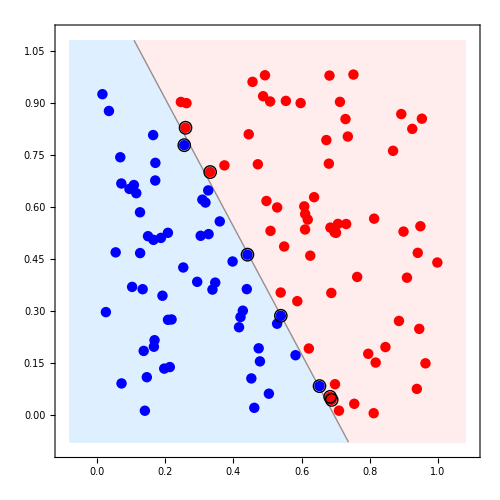

-Graphics3D-

```mathematica
<<SVM-Demos/DataSet1/DataSet1_C_1000_lin.nb
PlotSVC[DataSet1]
Plot3D[SVM[{x,y}],{x,-0.1,1.1},{y,-0.1,1.1},PlotPoints->51,ImageSize→{500,Automatic}]
```

## Example 2: non-linear classification using the RBF kernel

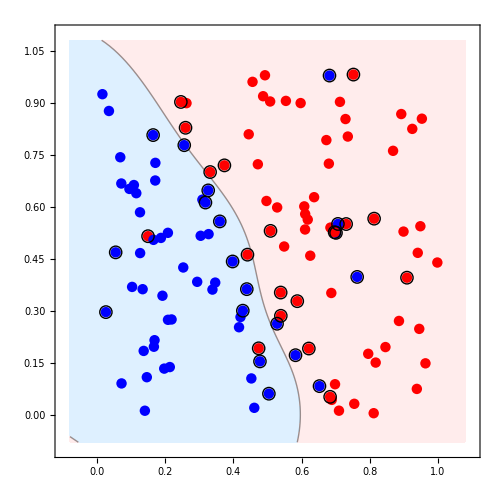

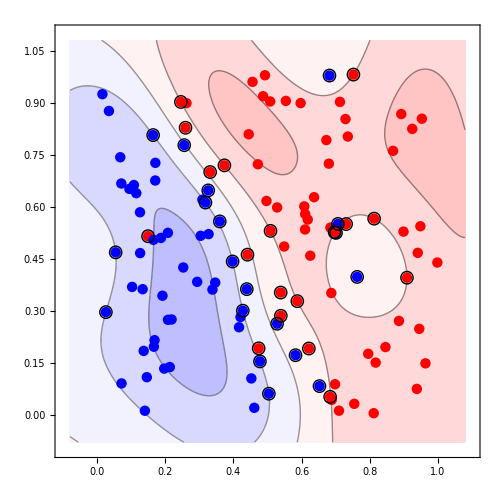

-Graphics3D-

```mathematica
<<SVM-Demos/DataSet4/DataSet4_C_10_rbf_10.nb
PlotSVC[DataSet4]
PlotSVCContour[DataSet4]
Plot3D[SVM[{x,y}],{x,-0.1,1.1},{y,-0.1,1.1},PlotPoints->51,ImageSize->{500,Automatic}]
```

## Example 3 : another non-linear classification using the RBF kernel

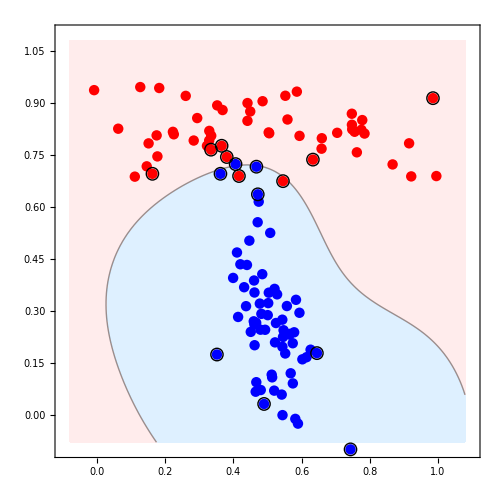

-Graphics3D-

```mathematica
<<SVM-Demos/DataSet6/DataSet6_C_10_rbf_10.nb
PlotSVC[DataSet6]
Plot3D[SVM[{x,y}],{x,-0.1,1.1},{y,-0.1,1.1},PlotPoints->51,ImageSize->{500,Automatic}]
```

## Example 4: support vector regression with RBF kernel

#### Pretty good solution

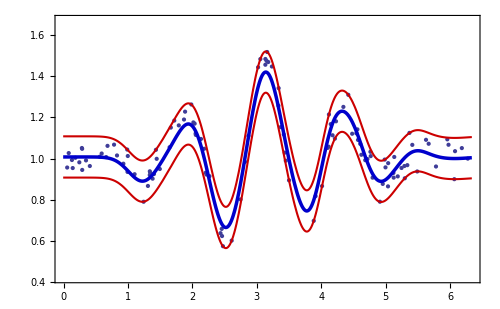

```mathematica
<<SVM-Demos/DataSet8/DataSet8_eps_0.1_C_100_rbf_10.nb
PlotSVR[DataSet8,0.1]
```

#### Scary overfitting!

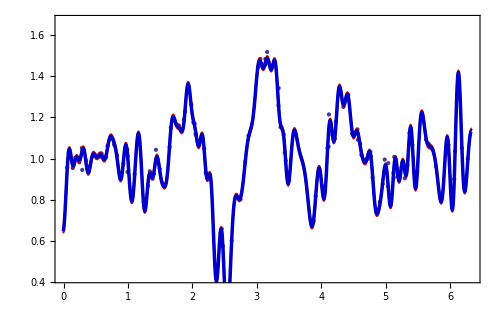

```mathematica
<<SVM-Demos/DataSet8/DataSet8_eps_0.01_C_100_rbf_100.nb
PlotSVR[DataSet8,0.01]
```